Decision Dependent Linear Regression Game

Performative Risk

```mathematica
PR1[t1_,t2_]:=0.5*(Subscript[β, 1] ᵀ.Subscript[Σ, 1].Subscript[β, 1]+Subscript[σ, 1]+(Subscript[μ, 1] ᵀ.t1+Subscript[γ, 1] ᵀ.t2)^2-2*(Subscript[β, 1] ᵀ.Subscript[Σ, 1].t1)+(t1ᵀ.Subscript[Σ, 1].t1))
PR2[t1_,t2_]:=0.5*(Subscript[β, 2] ᵀ.Subscript[Σ, 2].Subscript[β, 2]+Subscript[σ, 2]+(Subscript[μ, 2] ᵀ.t2+Subscript[γ, 2] ᵀ.t1)^2-2*(Subscript[β, 2] ᵀ.Subscript[Σ, 2].t2)+(t2ᵀ.Subscript[Σ, 2].t2))
J = {{D[PR1[Subscript[θ, 1],Subscript[θ, 2]],{Subscript[θ, 1],2}],D[PR1[Subscript[θ, 1],Subscript[θ, 2]],Subscript[θ, 1],Subscript[θ, 2]]},{D[PR2[Subscript[θ, 1],Subscript[θ, 2]],Subscript[θ, 1],Subscript[θ, 2]],D[PR2[Subscript[θ, 1],Subscript[θ, 2]],{Subscript[θ, 2],2}]}}
```

{{0.5 (2 (Transpose[μ_1].1)^2+2 Transpose'[θ_1].Σ_1.1+Transpose''[θ_1].Σ_1.θ_1),1. Transpose[γ_1].1 Transpose[μ_1].1},{1. Transpose[γ_2].1 Transpose[μ_2].1,0.5 (2 (Transpose[μ_2].1)^2+2 Transpose'[θ_2].Σ_2.1+Transpose''[θ_2].Σ_2.θ_2)}}

Initialization
The following initialization matches the game in the iPython notebooks with np.random.seed(10)

```mathematica
Subscript[d, 1]=2;
Subscript[d, 2]=2;
Subscript[Σ, 1]=IdentityMatrix[Subscript[d, 1]];
Subscript[Σ, 2]= IdentityMatrix[Subscript[d, 2]];
Subscript[σ, 1]=0.1;
Subscript[σ, 2]= 0.1;
Subscript[β, 1]={{1.3315865,0.71527897}}ᵀ;
Subscript[β, 2]={{-1.54540029,-0.00838385}}ᵀ;
Subscript[μ, 1]={{0.19598547,-0.22713365}}ᵀ;
Subscript[γ, 1]={{0.27768968, 0.11352727}}ᵀ;
Subscript[μ, 2]={{0.00737136,-0.29990942}}ᵀ;
Subscript[γ, 2]={{0.10160187, 0.28227125}}ᵀ;
(*Subscript[μ, 2]={{0.12668549, 0.2551389}}ᵀ;
Subscript[γ, 2]={{.21231995, 0.18378022}}ᵀ;*)
```

Closed Form Performative Optimum Calculation

```mathematica
Subscript[θ, 1PO]=Inverse[IdentityMatrix[Subscript[d, 1]]-Subscript[μ, 1].Subscript[γ, 1] ᵀ.Inverse[Subscript[μ, 2].Subscript[μ, 2] ᵀ+Subscript[Σ, 2]].Subscript[μ, 2].Subscript[γ, 2] ᵀ].Inverse[Subscript[μ, 1].Subscript[μ, 1] ᵀ+Subscript[Σ, 1]].(Subscript[Σ, 1].Subscript[β, 1]-Subscript[μ, 1].Subscript[γ, 1] ᵀ.Inverse[Subscript[μ, 2].Subscript[μ, 2] ᵀ+Subscript[Σ, 2]].Subscript[Σ, 2].Subscript[β, 2])
Subscript[θ, 2PO]=Inverse[IdentityMatrix[Subscript[d, 2]]-Subscript[μ, 2].Subscript[γ, 2] ᵀ.Inverse[Subscript[μ, 1].Subscript[μ, 1] ᵀ+Subscript[Σ, 1]].Subscript[μ, 1].Subscript[γ, 1] ᵀ].Inverse[Subscript[μ, 2].Subscript[μ, 2] ᵀ+Subscript[Σ, 2]].(Subscript[Σ, 2].Subscript[β, 2]-Subscript[μ, 2].Subscript[γ, 2] ᵀ.Inverse[Subscript[μ, 1].Subscript[μ, 1] ᵀ+Subscript[Σ, 1]].Subscript[Σ, 1].Subscript[β, 1])
```

{{1.38939},{0.648291}}

{{-1.54752},{0.0779318}}

Social Optimum Calculation

```mathematica
SR[t1_,t2_]:=Flatten[PR1[t1,t2]+PR2[t1,t2]]
Minimize[SR[{{t11,t12}}ᵀ,{{t21,t22}}ᵀ],{t11,t12,t21,t22}];
Subscript[θ, 1SO]={{%[[2,1,2]]},{%[[2,2,2]]}}
Minimize[SR[{{t11,t12}}ᵀ,{{t21,t22}}ᵀ],{t11,t12,t21,t22}];
Subscript[θ, 2SO]={{%[[2,3,2]]},{%[[2,4,2]]}}
```

{{1.35682},{0.581561}}

{{-1.47398},{0.0999326}}

Performative Risk at Nash

```mathematica
PR1[Subscript[θ, 1PO],Subscript[θ, 2PO]]
PR2[Subscript[θ, 1PO],Subscript[θ, 2PO]]
```

{{0.0976726}}

{{0.0955974}}

Performative Risk at Social Optimum

```mathematica
PR1[Subscript[θ, 1SO],Subscript[θ, 2SO]]
PR2[Subscript[θ, 1SO],Subscript[θ, 2SO]]
```

{{0.0941431}}

{{0.0925237}}

Contour Plots of Performative Risk
PR is plotted for each player with the other player’s strategy held constant at the performatively optimal value
Red points show the performatively optimal strategies, and the green points show the socially optimal strategies.

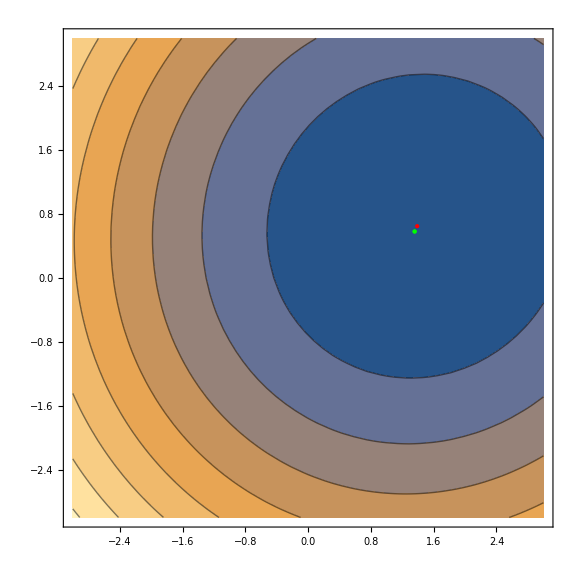
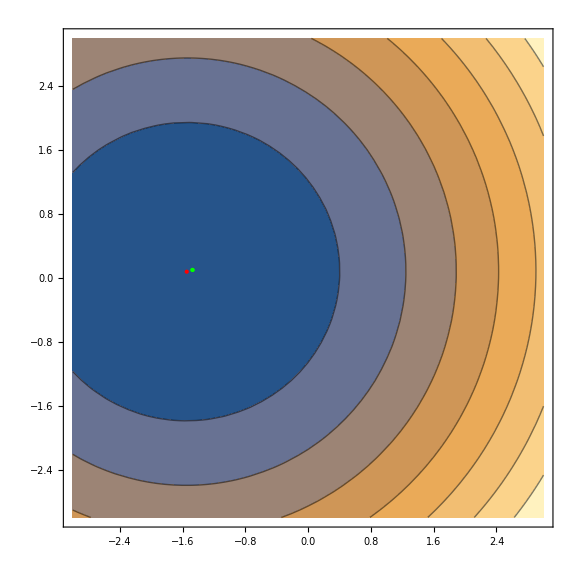
Row[-Graphics-,-Graphics-]

```mathematica
c1 = ContourPlot[PR1[{{t11},{t12}},Subscript[θ, 2PO]],{t11,-3,3},{t12,-3,3},
Epilog->{PointSize[Medium],Red,Point[{Flatten[Subscript[θ, 1PO] ᵀ]}]},
ImageSize->Large];
p1 = ListPlot[{Flatten[Subscript[θ, 1SO] ᵀ]},PlotStyle->{PointSize[Medium],Green},ImageSize->Large];
c2 = ContourPlot[PR2[Subscript[θ, 1PO],{{t21},{t22}}],{t21,-3,3},{t22,-3,3},
Epilog->{PointSize[Medium],Red,Point[{Flatten[Subscript[θ, 2PO] ᵀ]}]},
ImageSize->Large];
p2 = ListPlot[{Flatten[Subscript[θ, 2SO] ᵀ]},PlotStyle->{PointSize[Medium],Green},ImageSize->Large];
Row[Show[c1,p1],Show[c2,p2]]
```

Potential Game
The game is a potential game iff   

Calculating by hand,   

So the game is a potential game iff  

This is verified below:

```mathematica
{{D[PR1[Subscript[θ, 1],Subscript[θ, 2]],{Subscript[θ, 1],2}],D[PR1[Subscript[θ, 1],Subscript[θ, 2]],Subscript[θ, 1],Subscript[θ, 2]]},{D[PR2[Subscript[θ, 1],Subscript[θ, 2]],Subscript[θ, 1],Subscript[θ, 2]],D[PR2[Subscript[θ, 1],Subscript[θ, 2]],{Subscript[θ, 2],2}]}}
D[PR1[Subscript[θ, 1],Subscript[θ, 2]],{Subscript[θ, 1],2}]
D[PR1[Subscript[θ, 1],Subscript[θ, 2]],Subscript[θ, 1],Subscript[θ, 2]]
D[PR2[Subscript[θ, 1],Subscript[θ, 2]],Subscript[θ, 1],Subscript[θ, 2]]
D[PR2[Subscript[θ, 1],Subscript[θ, 2]],{Subscript[θ, 2],2}]
```

{{{{0.5 (-2 ({{0,0}}.1+{{0,0}}.θ_1)+2 ({{0,0}}.θ_1+{{0.195985,-0.227134}}.1)^2+2 ({{0,0}}.1+{{0,0}}.θ_1) ({{0.195985,-0.227134}}.θ_1+{{0.27769,0.113527}}.θ_2)+2 Transpose[θ_1].{{0,0},{0,0}}.1+Transpose[θ_1].{{0,0},{0,0}}.θ_1+2 Transpose'[θ_1].{{0,0},{0,0}}.θ_1+2 Transpose'[θ_1].{{1,0},{0,1}}.1+Transpose''[θ_1].{{1,0},{0,1}}.θ_1)}},{{1. ({{0,0}}.θ_1+{{0.195985,-0.227134}}.1) ({{0,0}}.θ_2+{{0.27769,0.113527}}.1)}}},{{{1. ({{0,0}}.θ_2+{{0.00737136,-0.299909}}.1) ({{0,0}}.θ_1+{{0.101602,0.282271}}.1)}},{{0.5 (-2 ({{0,0}}.1+{{0,0}}.θ_2)+2 ({{0,0}}.θ_2+{{0.00737136,-0.299909}}.1)^2+2 ({{0,0}}.1+{{0,0}}.θ_2) ({{0.00737136,-0.299909}}.θ_2+{{0.101602,0.282271}}.θ_1)+2 Transpose[θ_2].{{0,0},{0,0}}.1+Transpose[θ_2].{{0,0},{0,0}}.θ_2+2 Transpose'[θ_2].{{0,0},{0,0}}.θ_2+2 Transpose'[θ_2].{{1,0},{0,1}}.1+Transpose''[θ_2].{{1,0},{0,1}}.θ_2)}}}}

{{0.5 (-2 ({{0,0}}.1+{{0,0}}.θ_1)+2 ({{0,0}}.θ_1+{{0.195985,-0.227134}}.1)^2+2 ({{0,0}}.1+{{0,0}}.θ_1) ({{0.195985,-0.227134}}.θ_1+{{0.27769,0.113527}}.θ_2)+2 Transpose[θ_1].{{0,0},{0,0}}.1+Transpose[θ_1].{{0,0},{0,0}}.θ_1+2 Transpose'[θ_1].{{0,0},{0,0}}.θ_1+2 Transpose'[θ_1].{{1,0},{0,1}}.1+Transpose''[θ_1].{{1,0},{0,1}}.θ_1)}}

{{1. ({{0,0}}.θ_1+{{0.195985,-0.227134}}.1) ({{0,0}}.θ_2+{{0.27769,0.113527}}.1)}}

{{1. ({{0,0}}.θ_2+{{0.00737136,-0.299909}}.1) ({{0,0}}.θ_1+{{0.101602,0.282271}}.1)}}

{{0.5 (-2 ({{0,0}}.1+{{0,0}}.θ_2)+2 ({{0,0}}.θ_2+{{0.00737136,-0.299909}}.1)^2+2 ({{0,0}}.1+{{0,0}}.θ_2) ({{0.00737136,-0.299909}}.θ_2+{{0.101602,0.282271}}.θ_1)+2 Transpose[θ_2].{{0,0},{0,0}}.1+Transpose[θ_2].{{0,0},{0,0}}.θ_2+2 Transpose'[θ_2].{{0,0},{0,0}}.θ_2+2 Transpose'[θ_2].{{1,0},{0,1}}.1+Transpose''[θ_2].{{1,0},{0,1}}.θ_2)}}